3) Решить уравнение Лапласа в двумерном пространстве методом граничных элементов. Геометрия задачи - такая же, как и на семинаре (размеры указаны в метрах). Граничные условия:

Прямоугольник - металл, потенциал 1В
Диск - поле 2 В/м
Треугольник - металл, полный заряд 1нКл

```mathematica
Clear["Global`*"];
```

```mathematica
QQ=10^-9;(*C*)
ϵ0=8.85×10^-12;(*F/m*)
```

```mathematica
Geometry={Disk[],Rectangle[{1,2},{7,4}],Triangle[{{3,0},{6,1},{2,-1.5}}]};
HighlightMesh[bMesh=BoundaryMesh[DiscretizeRegion[RegionUnion@@Geometry,MaxCellMeasure->0.05]],Labeled[0,"Index"]]
NEl=MeshCellCount[%,1]
```

-Graphics-

102

```mathematica
GreenF[x_,x0_]:=-N[1/(2 π) Log[Norm[x-x0]]];
DGreenF[x_,x0_]:=-N[1/(2 π Norm[x-x0])];
```

```mathematica
BElts=MeshPrimitives[bMesh,1];
Knots=RegionCentroid/@BElts;
Measure=RegionMeasure/@BElts;
Segment=ParallelTable[BElts[[i,1,2]]-BElts[[i,1,1]],{i,1,NEl}];
```

```mathematica
TriangleInd=Select[Range[NEl],6≥ Knots[[#,1]]≥ 2 && -1.5≤ Knots[[#,2]]≤1 &];
RectangleInd=Select[Range[NEl],Knots[[#,1]]≥ 0.9 && 1.5≤ Knots[[#,2]]≤4.5 &];
DiskInd= Select[Range[NEl],Knots[[#,1]]≤1 && Knots[[#,2]]≤1 &];
```

```mathematica
G=ParallelTable[If[i!=j,NIntegrate[GreenF[Knots[[i]],BElts[[j,1,1]]+t Segment[[j]]],{t,0,1}],0],{i,1,NEl},{j,1,NEl}];
G=Transpose[Measure×Transpose[G]]+DiagonalMatrix[Table[#/π(1-Log[#])&[Measure[[i]]/2] ,{i,1,NEl}]];
G=Chop[G];
```

```mathematica
Off[NIntegrate::izero];
H=Transpose[
Measure×
Transpose[ParallelTable[If[i!=j,NIntegrate[({-#[[2]],#[[1]]}/Measure[[j]]&[Segment[[j]]]).(#/Norm[#]&[BElts[[j,1,1]]+t Segment[[j]]-Knots[[i]]])DGreenF[Knots[[i]],BElts[[j,1,1]]+t Segment[[j]]],{t,0,1}],0],{i,1,NEl},{j,1,NEl}]]];
H=H+1/2 IdentityMatrix[NEl];
H=Chop[H];
```

```mathematica
u =Table[Subscript[U, i],{i,1,NEl}];
u[[RectangleInd]]=1;
u[[TriangleInd]]=U;
```

```mathematica
q =Table[Subscript[Q, i],{i,1,NEl}];
q[[DiskInd]]=2;
```

```mathematica
unknown=DeleteDuplicates[Select[Flatten[Append[u,q]],Not[NumericQ[#]]&]];
```

```mathematica
mainEquation=G.q==H.u;
```

```mathematica
electricFlux=Total[ParallelTable[
Cross[
Append[Subscript[Q, i]({-#[[2]],#[[1]]}/Measure[[i]]&[Segment[[i]]]),0],
Append[Segment[[i]],0]
][[3]]
,{i,TriangleInd}]];
```

```mathematica
gaussEquation=-QQ/ϵ0==electricFlux;
```

```mathematica
s=Solve[{mainEquation,gaussEquation},unknown];
```

```mathematica
u=u/.s[[1]];
```

```mathematica
q=q/.s[[1]];
```

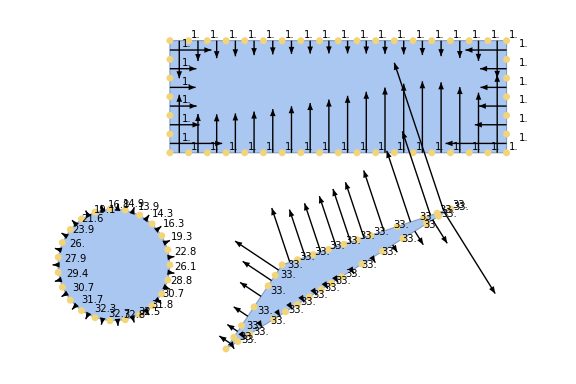

```mathematica
Show[
HighlightMesh[bMesh,0,ImageSize->Large],
Graphics[{
Arrowheads[.02],
ParallelTable[
Arrow[{
Knots[[i]],
Knots[[i]]-0.05×q[[i]]{-#[[2]],#[[1]]}/Norm[#]&[Segment[[i]]]
}],
{i,1,NEl}]}
],
Graphics[ParallelTable[Text[Style[Round[u[[i]],0.1],Black,10],Knots[[i]]+{0.3,0.1}],{i,1,NEl}]]]
```